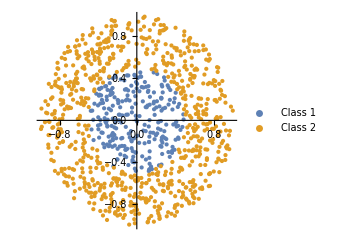

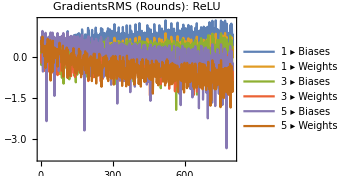
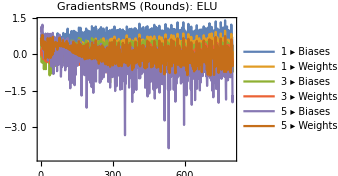
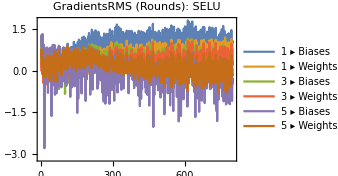
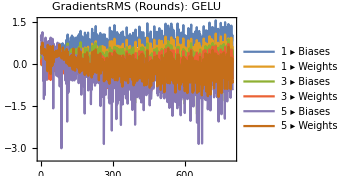
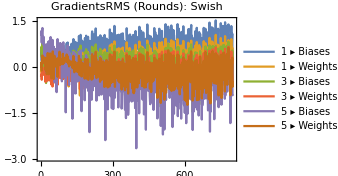
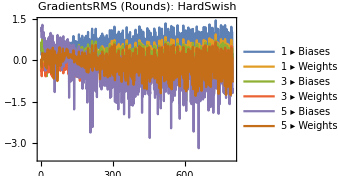
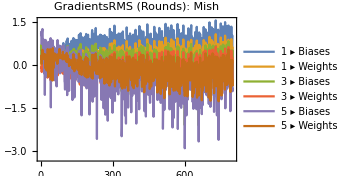

```mathematica
(* The code aims to generate synthetic training data points within a unit disk, label them based on their distance from the origin,and visualize the training set to inspect the data distribution. It then evaluates the performance of various activation functions in a neural network by training the network using each function. The neural network, defined with two hidden layers and an output layer using a logistic sigmoid activation,is trained on the synthetic data using the ADAM optimization method, with training progress monitored through the GradientsRMS property. The results,including the evolution of GradientsRMS, are recorded for each activation function to compare their effectiveness,providing insights into their impact on the training dynamics and classification performance,thus aiding in the selection of suitable activation functions for future neural network designs: *)

(* Generate 1000 random points within a unit disk for training: *)
trainpoints=RandomPoint[Disk[],1000];

(* Assign labels based on whether the point's distance from the origin is less than 0.5: *)
trainlabels=Thread[Map[Norm,trainpoints]<0.5];

(* Combine the points and labels into training data: *)
trainingData=trainpoints->trainlabels;

(* Visualize the synthetic training set with different colors for each class: *)
ListPlot[
{
Pick[trainpoints,trainlabels,True],
Pick[trainpoints,trainlabels,False]
},
AspectRatio->1,
ImageSize->250,
PlotStyle->PointSize[Medium],
FrameLabel->{"X","Y","Synthetic Training Set"},
PlotLegends->{"Class 1","Class 2"}
]

(* Set up array for activation functions  *)
activationFunctions={
"ReLU","ELU","SELU",
"GELU","Swish","HardSwish",
"Mish","SoftPlus","HardTanh",
"HardSigmoid","Sigmoid",Tanh
} ;

(* Loop through each activation function, train a neural network, and record the results: *)
results=Table[
Module[
{net,trainedNet},

(* Define a simple neural network structure: *)
net=NetChain[
{
(* First hidden layer with specified activation function: *)
LinearLayer[5],ElementwiseLayer[functions],
(* Second hidden layer with specified activation function: *)
LinearLayer[5],ElementwiseLayer[functions],
(* Output layer with logistic sigmoid activation function: *)
LinearLayer[],ElementwiseLayer[LogisticSigmoid]  
},
"Output"->NetDecoder["Boolean"]
];

(* Train the network on training data: *)
trainedNet=NetTrain[
net,
trainingData,
(* Monitor training progress using GradientsRMS property: *)
<|
"Property"->"GradientsRMS",
"Form"->"EvolutionPlot",
"PlotOptions"->{ PlotLabel->Style[Row[{"GradientsRMS (Rounds): ",functions}],12,Bold],ImageSize->250},
"Interval"->"Batch"
|>,

(* Set the batch size for training: *)
BatchSize->64,
(* Learning rate for "ADAM": *)
LearningRate->0.01,
(* Use "ADAM" as the optimization method: *)
Method->"ADAM",
(* Maximum number of training iterations: *)
MaxTrainingRounds->50
]
],
(* Iterate over the grid of activation functions: *)
{functions,activationFunctions}
]
```

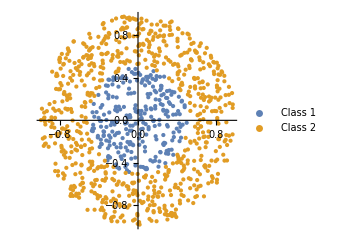

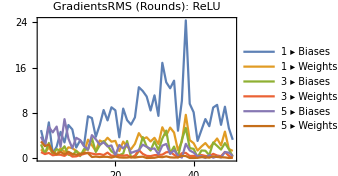
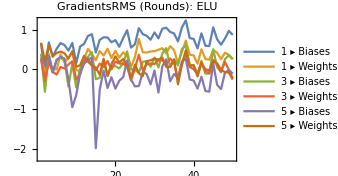
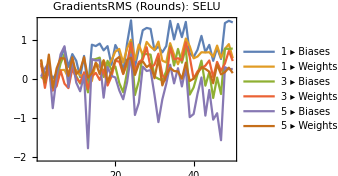
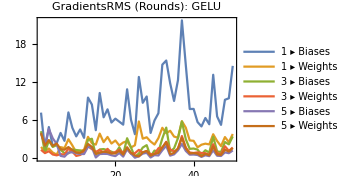
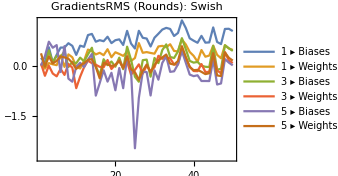
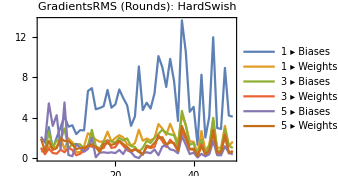
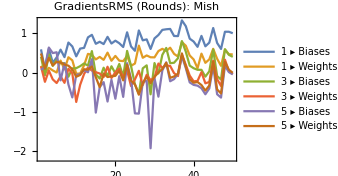

```mathematica
(* The above and the following codes are largely similar, both aiming to generate synthetic training data, train a neural network using various activation functions,and monitor the training process. However, they differ in how they monitor the training progress: the above code monitors the GradientsRMS property at the "Batch" interval,providing a more granular view of the gradient changes, while the following code monitors it at the "Rounds" interval, offering a broader view: *)

(* Generate 1000 random points within a unit disk for training: *)
trainpoints=RandomPoint[Disk[],1000];

(* Assign labels based on whether the point's distance from the origin is less than 0.5: *)
trainlabels=Thread[Map[Norm,trainpoints]<0.5];

(* Combine the points and labels into training data: *)
trainingData=trainpoints->trainlabels;

(* Visualize the synthetic training set with different colors for each class: *)
ListPlot[
{
Pick[trainpoints,trainlabels,True],
Pick[trainpoints,trainlabels,False]
},
AspectRatio->1,
ImageSize->250,
PlotStyle->PointSize[Medium],
FrameLabel->{"X","Y","Synthetic Training Set"},
PlotLegends->{"Class 1","Class 2"}
]

(* Set up array for activation functions  *)
activationFunctions={
"ReLU","ELU","SELU",
"GELU","Swish","HardSwish",
"Mish","SoftPlus","HardTanh",
"HardSigmoid","Sigmoid",Tanh
} ;

(* Loop through each activation function, train a neural network, and record the results: *)
results=Table[
Module[
{net,trainedNet},

(* Define a simple neural network structure: *)
net=NetChain[
{
(* First hidden layer with specified activation function: *)
LinearLayer[5],ElementwiseLayer[functions],
(* Second hidden layer with specified activation function: *)
LinearLayer[5],ElementwiseLayer[functions],
(* Output layer with logistic sigmoid activation function: *)
LinearLayer[],ElementwiseLayer[LogisticSigmoid]  
},
"Output"->NetDecoder["Boolean"]
];

(* Train the network on training data: *)
trainedNet=NetTrain[
net,
trainingData,
(* Monitor training progress using GradientsRMS property: *)
<|
"Property"->"GradientsRMS",
"Form"->"EvolutionPlot",
"PlotOptions"->{ PlotLabel->Style[Row[{"GradientsRMS (Rounds): ",functions}],12,Bold],ImageSize->250},
"Interval"->"Rounds"
|>,

(* Set the batch size for training: *)
BatchSize->64,
(* Learning rate for "ADAM": *)
LearningRate->0.01,
(* Use "ADAM" as the optimization method: *)
Method->"ADAM",
(* Maximum number of training iterations: *)
MaxTrainingRounds->50
]
],
(* Iterate over the grid of activation functions: *)
{functions,activationFunctions}
]
```

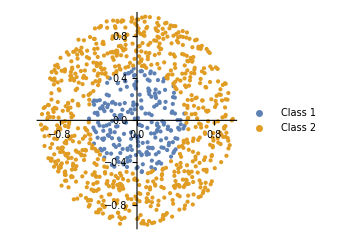

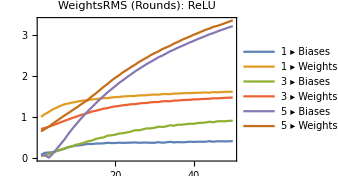
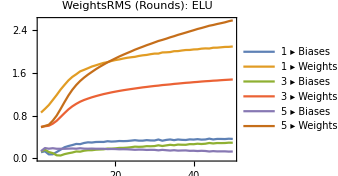
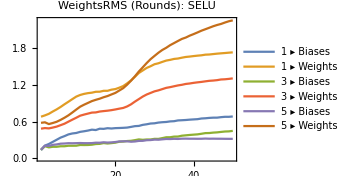
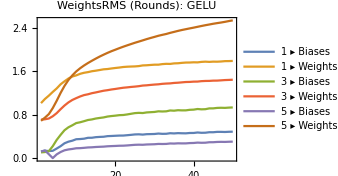
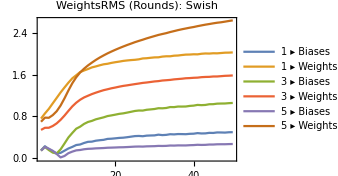
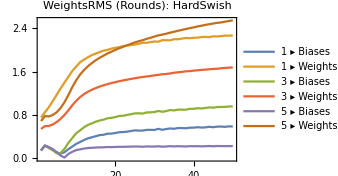
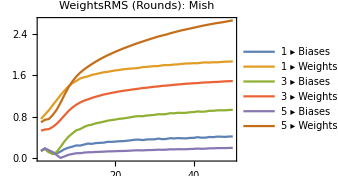

```mathematica
(* The above and the following codes are largely similar, both aiming to generate synthetic training data, train a neural network using various activation functions,and monitor the training process. In this case, training progress is monitored using the WeightsRMS property at the "Rounds" interval: *)

(* Generate 1000 random points within a unit disk for training: *)
trainpoints=RandomPoint[Disk[],1000];

(* Assign labels based on whether the point's distance from the origin is less than 0.5: *)
trainlabels=Thread[Map[Norm,trainpoints]<0.5];

(* Combine the points and labels into training data: *)
trainingData=trainpoints->trainlabels;

(* Visualize the synthetic training set with different colors for each class: *)
ListPlot[
{
Pick[trainpoints,trainlabels,True],
Pick[trainpoints,trainlabels,False]
},
AspectRatio->1,
ImageSize->250,
PlotStyle->PointSize[Medium],
FrameLabel->{"X","Y","Synthetic Training Set"},
PlotLegends->{"Class 1","Class 2"}
]

(* Set up array for activation functions  *)
activationFunctions={
"ReLU","ELU","SELU",
"GELU","Swish","HardSwish",
"Mish","SoftPlus","HardTanh",
"HardSigmoid","Sigmoid",Tanh
} ;

(* Loop through each activation function, train a neural network, and record the results: *)
results=Table[
Module[
{net,trainedNet},

(* Define a simple neural network structure: *)
net=NetChain[
{
(* First hidden layer with specified activation function: *)
LinearLayer[5],ElementwiseLayer[functions],
(* Second hidden layer with specified activation function: *)
LinearLayer[5],ElementwiseLayer[functions],
(* Output layer with logistic sigmoid activation function: *)
LinearLayer[],ElementwiseLayer[LogisticSigmoid]  
},
"Output"->NetDecoder["Boolean"]
];

(* Train the network on training data: *)
trainedNet=NetTrain[
net,
trainingData,
(* Monitor training progress using WeightsRMS property: *)
<|
"Property"->"WeightsRMS",
"Form"->"EvolutionPlot",
"PlotOptions"->{ PlotLabel->Style[Row[{"WeightsRMS (Rounds): ",functions}],12,Bold],
ImageSize->250},
"Interval"->"Rounds"
|>,
(* Set the batch size for training: *)
BatchSize->64,
(* Learning rate for "ADAM": *)
LearningRate->0.01,
(* Use "ADAM" as the optimization method: *)
Method->"ADAM",
(* Maximum number of training iterations: *)
MaxTrainingRounds->50
]
],
(* Iterate over the grid of activation functions: *)
{functions,activationFunctions}
]
```

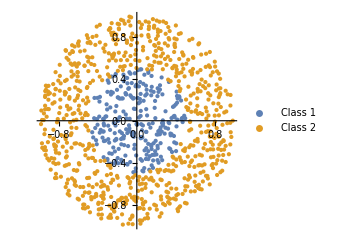

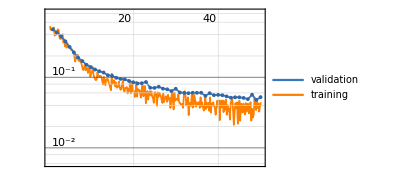
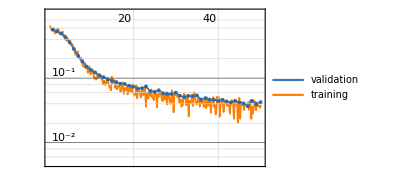
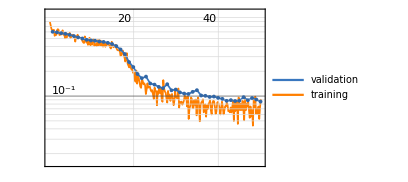
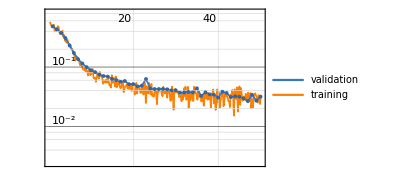
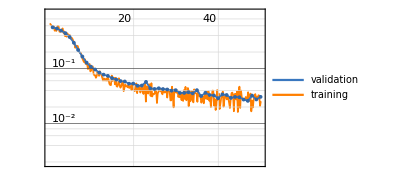
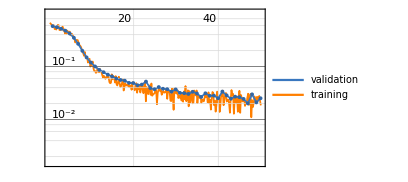
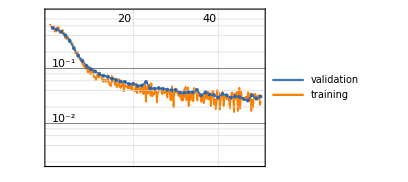
{ | rounds
loss | -Graphics-ReLU, | rounds
loss | -Graphics-ELU, | rounds
loss | -Graphics-SELU, | rounds
loss | -Graphics-GELU, | rounds
loss | -Graphics-Swish, | rounds
loss | -Graphics-HardSwish, | rounds
loss | -Graphics-Mish, | rounds
loss | -Graphics-SoftPlus, | rounds
loss | -Graphics-HardTanh, | rounds
loss | -Graphics-HardSigmoid, | rounds
loss | -Graphics-Sigmoid, | rounds
loss | -Graphics-Tanh}

{{ReLU,0.0522567},{ELU,0.0425113},{SELU,0.085622},{GELU,0.0317486},{Swish,0.0305856},{HardSwish,0.0252825},{Mish,0.0310274},{SoftPlus,0.0538208},{HardTanh,0.473651},{HardSigmoid,0.100753},{Sigmoid,0.15248},{Tanh,0.0587848}}

{{ReLU,0.978},{ELU,0.986},{SELU,0.97},{GELU,0.994},{Swish,0.996},{HardSwish,0.992},{Mish,0.996},{SoftPlus,0.988},{HardTanh,0.714},{HardSigmoid,0.956},{Sigmoid,0.938},{Tanh,0.982}}

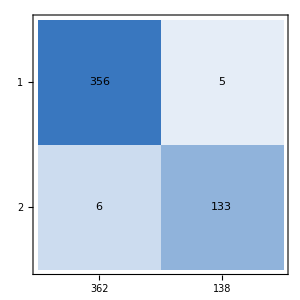
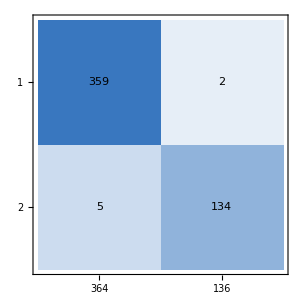
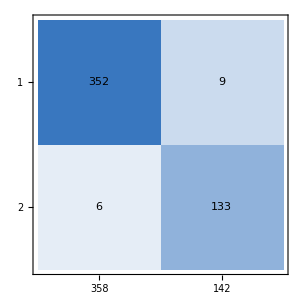
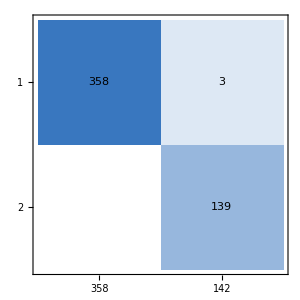
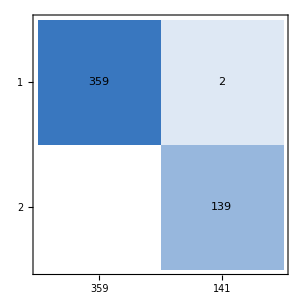
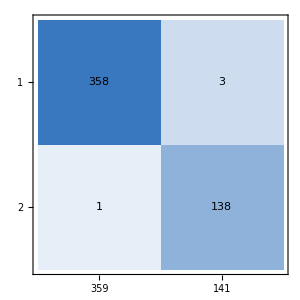
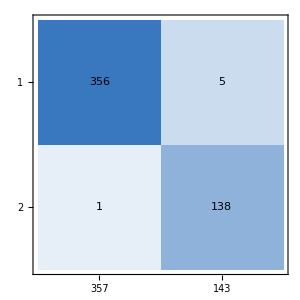
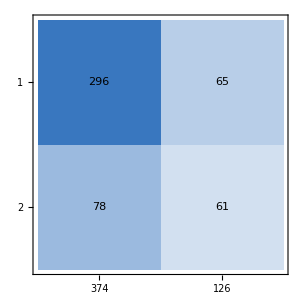
{actual class | -Graphics-
 | predicted classReLU,actual class | -Graphics-
 | predicted classELU,actual class | -Graphics-
 | predicted classSELU,actual class | -Graphics-
 | predicted classGELU,actual class | -Graphics-
 | predicted classSwish,actual class | -Graphics-
 | predicted classHardSwish,actual class | -Graphics-
 | predicted classMish,actual class | -Graphics-
 | predicted classSoftPlus,actual class | -Graphics-
 | predicted classHardTanh,actual class | -Graphics-
 | predicted classHardSigmoid,actual class | -Graphics-
 | predicted classSigmoid,actual class | -Graphics-
 | predicted classTanh}

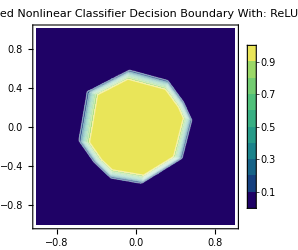
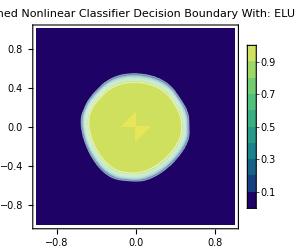
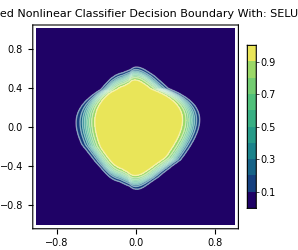
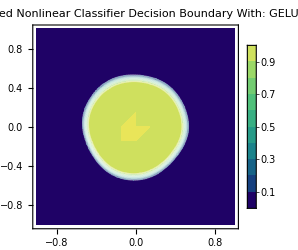
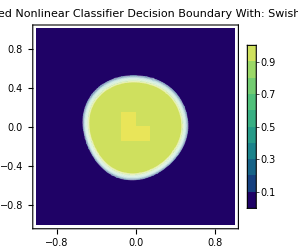
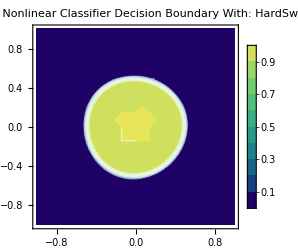
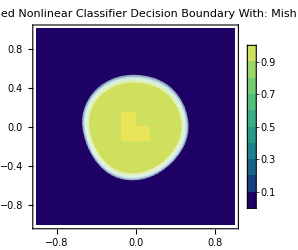
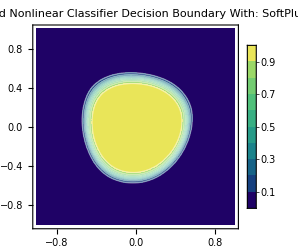

```mathematica
(* The code aims to generate synthetic training and validation data points within a unit disk,assigning binary labels based on their distance from the origin. It visualizes the training set to inspect data distribution and evaluates various activation functions in a neural network by systematically training and validating the network using each function. The neural network,with two hidden layers and an output layer using logistic sigmoid activation, is trained using the ADAM optimization method,with progress monitored through accuracy and confusion matrix plots. Results, including validation accuracy, confusion matrices, and loss plots,are recorded and compared for each activation function. The decision boundaries of the trained networks are visualized to understand the influence of each activation function,providing insights into their impact on the training dynamics and classification performance, aiding in selecting suitable activation functions for future designs: *)

(* Generate 1000 random points within a unit disk for training: *)
trainpoints=RandomPoint[Disk[],1000];

(* Assign labels based on whether the point's distance from the origin is less than 0.5: *)
trainlabels=Thread[Map[Norm,trainpoints]<0.5];

(* Combine the points and labels into training data: *)
trainingData=trainpoints->trainlabels;

(* Generate 500 random points within a unit disk for validation: *)
validationPoints=RandomPoint[Disk[],500];

(* Assign labels using the same criteria as for the training set: *)
validationLabels=Thread[Map[Norm,validationPoints]<0.5];

(* Combine the points and labels into validation data: *)
validationData=validationPoints->validationLabels;

(* Visualize the synthetic training set with different colors for each class: *)
ListPlot[
{
Pick[trainpoints,trainlabels,True],
Pick[trainpoints,trainlabels,False]
},
AspectRatio->1,
ImageSize->250,
PlotStyle->PointSize[Medium],
FrameLabel->{"X","Y","Synthetic Training Set"},
PlotLegends->{"Class 1","Class 2"}
]

(* Set up array for activation functions  *)
activationFunctions={
"ReLU","ELU","SELU",
"GELU","Swish","HardSwish",
"Mish","SoftPlus","HardTanh",
"HardSigmoid","Sigmoid",Tanh
} ;

(* Loop through each activation function, train a neural network, and record the results: *)
results=Table[
Module[
{net,trainedNet},

(* Define a simple neural network structure: *)
net=NetChain[
{
(* First hidden layer with specified activation function: *)
LinearLayer[5],ElementwiseLayer[functions],
(* Second hidden layer with specified activation function: *)
LinearLayer[5],ElementwiseLayer[functions],
(* Output layer with logistic sigmoid activation function: *)
LinearLayer[],ElementwiseLayer[LogisticSigmoid]  
},
"Output"->NetDecoder["Boolean"]
];

(* Train the network on training data and validate it: *)
trainedNet=NetTrain[
net,
trainingData,
All,
(* Use validation data for monitoring performance: *)
ValidationSet->validationData,
(* Monitor accuracy and confusion matrix during training: *)
TrainingProgressMeasurements->{"Accuracy","ConfusionMatrixPlot"},
(* Set the batch size for training: *)
BatchSize->64,
(* Learning rate for "ADAM": *)
LearningRate->0.01,
(* Use "ADAM" as the optimization method: *)
Method->"ADAM",
(* Maximum number of training iterations: *)
MaxTrainingRounds->50
];
(* Extract validation measurements from training results: *)
validationMeasurements=trainedNet["ValidationMeasurements"];
(* Get the loss plot from training results: *)
lossplot=trainedNet["LossPlot"];
(* Get the trained network: *)
trainednet=trainedNet["TrainedNet"];
(* Return validation measurements,loss plot,and trained network: *)
{validationMeasurements,lossplot,trainednet}
],
(* Iterate over the grid of activation functions: *)
{functions,activationFunctions}
];

(* Display LossPlot for each activation function: *)
Table[
Overlay[{results[[i]][[2]],activationFunctions[[i]]},Alignment->{0.9,0.4}],
{i,1,12}
]

(* Display Loss for each activation function:*)
Table[
{activationFunctions[[i]],results[[i]][[1]][[1]]},
{i,1,12}
]

(* Display validation accuracy for each activation function: *)
Table[
{activationFunctions[[i]],results[[i]][[1]][[2]]},
{i,1,12}
]

(* Display ConfusionMatrixPlot for each activation function:*)
Table[
Overlay[{results[[i]][[1]][[3]],activationFunctions[[i]]},Alignment->{0.7,0.8}],
{i,1,12}
]

(* Visualize the decision boundary of the trained network: *)
Table[
ContourPlot[
results[[i]][[3]][{x,y},None],
{x,-1,1},
{y,-1,1},
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic,
LabelStyle->Directive[Black,12],
ImageSize->250,
PlotLabel->Style[Row[{"Trained Nonlinear Classifier Decision \n Boundary With: ",activationFunctions[[i]]}],12,Bold]
],
{i,1,12}
]
```